The New Seeker

```mathematica
uniformInDball[n_:50000,d_:2]:=
Drop[#,2]&/@
Normalize/@
RandomVariate[
NormalDistribution[],{n,d+2}];
getTarget[d_:4]:=uniformInDball[1,d]⟦1⟧;
sowSkipper=0;
sowSkipModulus=200;
drawSigmaCircles=True;
drawArrows=False;
sowSkip=If[Mod[(sowSkipper++),sowSkipModulus]===0,Sow@#,Identity@#]&;
deathTest=True;
doJudgment[{yp_,dist_,σ_},{Δ_,tar_,tol_,maxIter_,i_}]:=
With[{},
If[(deathTest && (dist>10maxIter σ)),Throw[{yp,dist,σ,tar,Δ,i},"Dead"]];
If[i≥maxIter,Throw[{yp,dist,σ,tar,Δ,i},"Wandering"]]; 
With[{a=Map[RandomVariate[NormalDistribution[#,σ]]&,yp]},
With[{da=EuclideanDistance[tar,a]},
If[da<tol,Throw[{a,da,σ,tar,Δ,i},"Found"]];
With[{b=Map[RandomVariate[NormalDistribution[#,σ]]&,yp]},
With[{db=EuclideanDistance[tar,b]},
If[db<tol,Throw[{b,db,σ,tar,Δ,i},"Found"]];
With[{νσ=Quiet[σ*Δ]},
sowSkip@If[da<db,{a,da,νσ},{b,db,νσ}]]]]]]];
trialDict[{yp_,dist_,σ_,tar_,Δ_,i_},tag_]:=
<|"yp"->yp,"dist"->dist,"σ"->σ,"tar"->tar,"Δ"->Δ,"i"->i,"tag"->tag|>;
picker[n_]:=#⟦n⟧&;{yp,dist,σ}=picker/@Range[3];
echo=Echo;
DBALLRADIUS=1.0;
vizSeek2D002[tol_:0.1,Δ_:0.99599,maxIter_:10000,pr_:10,dim_:2]:=
(* For picking a random pair of dims for display from big-dim vectors. *)
With[{indices=Sort@RandomSample[Range[dim],2]},
With[{indexer={#⟦indices⟦1⟧⟧,#⟦indices⟦2⟧⟧}&},
With[{sampler={indexer[yp[#]],dist[#],σ[#]}&},
With[{tar=getTarget[dim],ini=ConstantArray[0,dim]},
sowSkipper=0;
With[{result=Reap[Catch[Catch[Catch[Fold[
doJudgment,{ini,0,DBALLRADIUS},(* algo step 2 *)
Table[{Δ,tar,tol,maxIter,i},{i,maxIter}]],
"Found",trialDict],"Dead",trialDict],"Wandering",trialDict]]},
With[{tag=result⟦1⟧["tag"],smtar=indexer@tar,sampled=sampler/@result⟦2,1⟧,l=result⟦1⟧["i"]},
last1=sampled[[1]];
Show[Graphics[{
LightGray,Disk[],White,Disk[smtar,0.3],Black,Circle[smtar,0.3],
MapIndexed[
{Hue[(2.+#2*4/Length[sampled])/6.],
If[drawSigmaCircles,Circle[yp[#1],σ[#1]]],
If[drawArrows,Line[{yp[last1],yp[#1]}]],
Point[yp[#1]],
last1=#1;}&,
sampled],
Text[Style[{l,tag(*,Δ,tol*),σ[Last[sampled]]},"Text",Background->White],{0,pr*0.960}]
}],AspectRatio->Automatic,Frame->True,PlotRange->1.025*pr]]]]]]];
```

```mathematica
Manipulate[
(sowSkipModulus=decimation;
drawSigmaCircles=drawSigmaCirclesLocal;
drawArrows=drawArrowsLocal;
vizSeek2D002[10.^le,1.-10^-ld,Floor[10.^lm],2^r,dim]),
Column[{Row[{Button["  DO AGAIN  ",(le++;le--)&],"    ",
Button["  RESET  ",(le=-2;ld=1.0;lm=2;r=2;dim=2;decimation=1;drawSigmaCircles=True;drawArrows=False)&],
"   draw sigma circles? ",Checkbox[Dynamic[drawSigmaCirclesLocal]],
"   draw arrows? ",Checkbox[Dynamic[drawArrowsLocal]]
}],
Control[{{le,-2,"log_10(tol)"},-5,0,0.1,Appearance->{"Open","Labeled"}}],
Control[{{ld,1.0,"-log_10(1-Δ)"},0.,5.,0.25,Appearance->{"Open","Labeled"}}],
Control[{{lm,3,"log_10(reps)"},0,7,1,Appearance->{"Open","Labeled"}}],
Control[{{r,1,"log_2 plot range"},-8,8,1,Appearance->{"Open","Labeled"}}],
Control[{{dim,2},{2,5,10,20,50,100,200,500,1000,2000,5000,10000},ControlType->Setter}],
Control[{{decimation,1},{1,2,5,10,20,50,100,200,500,1000,10000,100000},ControlType->Setter}]
}],
SaveDefinitions->True]
```

Search in D dimensions by pairwise preferences in a shrinking ball. The controls, from top to bottom, specify (1) log_10 of tolerance, the Euclidean distance within which a guess is reckoned successful; (2) the number of leading nines in Δ<1, which is the shrinkage factor for σ, the search radius; (3) log_10 of reps, the max number of iterations to devote to a search; (4) the plot range so that we can see the extend of the walk; (5) dim, the number of dimensions of Euclidean space. Only two dimensions are displayed, but those two are chosen randomly. Seeker picks a target point uniformly at random in the unit D-ball. That point is at the center of the white disk within the gray unit D-ball. Seeker's first two guesses, A, B, are drawn from the Normal distribution with mean zero and standard deviation 1, again represented by the gray disk. The nearer of the two guesses, Y=A or Y=B, to the target is retained and put at the center of a new pair drawn from a Normal distribution with mean Y and standard deviation Δ σ. The process recurses until one of the following occurs: (1) Wandering: the number of guesses exceeds the maximum specified by the third control; (2) Dead: the distance of the current search center Y from the target exceeds 10×σ×maxIter; this is a quick-exit heuristic that is important for runs in high dimensions; (3) Found: the distance of Y from the target is less than tolerance, specified by the first control. If all your searches die, consider increasing the second control, that is, consider shrinking the searches less rapidly. If none die, then shrink more rapidly, because you're probably searchnig more conservatively than you have to do. If all your searches wander, consider increasing maxIter, the third control, or decreasing the second control, that is, consider shrinking the searches more rapidly. With a little practice, you will develop an feel for

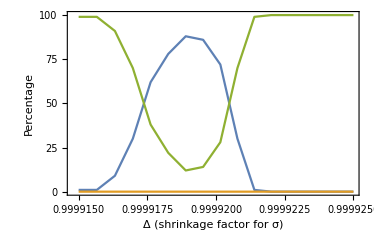
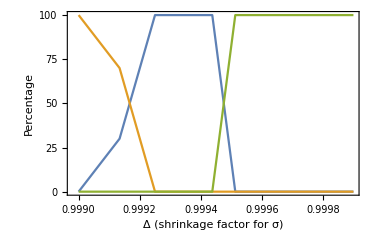

The charts above are summaries of 1,600 runs in each of 2,000 and 200 dimensions. It shows the percentage of searches that ended up wandering (green), that ended up dead (yellow), or that were successful (blue). For each setting of the controls, there is a "best" range of values for Δ, those being the ones that yield the largest percentage of Found versus Wandering or Dead. The chart in 2,000 dimensions took more than six hours to run with ParallelMap on six cores.

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX